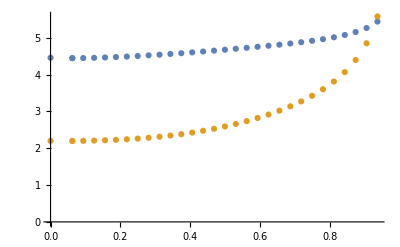

```mathematica
e={{0,4.455578},{0.062500,4.444360},{0.062500,4.444360},{0.093750,4.446884},{0.125000,4.453136},{0.156250,4.462229},{0.187500,4.473663},{0.218750,4.487116},{0.250000,4.502362},{0.281250,4.519238},{0.312500,4.537614},{0.343750,4.557382},{0.375000,4.578434},{0.406250,4.600662},{0.437500,4.623942},{0.468750,4.648136},{0.500000,4.673096},{0.531250,4.698703},{0.562500,4.724947},{0.593750,4.751971},{0.625000,4.780072},{0.656250,4.809690},{0.687500,4.841417},{0.718750,4.876037},{0.750000,4.914606},{0.781250,4.958592},{0.812500,5.010153},{0.843750,5.072700},{0.875000,5.152269},{0.906250,5.261673},{0.937500,5.436201}};
f={{0,2.199345},{0.062500,2.195900},{0.062500,2.195900},{0.093750,2.199482},{0.125000,2.205868},{0.156250,2.215057},{0.187500,2.227208},{0.218750,2.242576},{0.250000,2.261486},{0.281250,2.284318},{0.312500,2.311498},{0.343750,2.343476},{0.375000,2.380712},{0.406250,2.423641},{0.437500,2.472626},{0.468750,2.527939},{0.500000,2.589821},{0.531250,2.658637},{0.562500,2.734988},{0.593750,2.819698},{0.625000,2.913843},{0.656250,3.018848},{0.687500,3.136637},{0.718750,3.269857},{0.750000,3.422228},{0.781250,3.599175},{0.812500,3.809011},{0.843750,4.065408},{0.875000,4.393357},{0.906250,4.846924},{0.937500,5.575393}};
ListPlot[{e,f}]
```

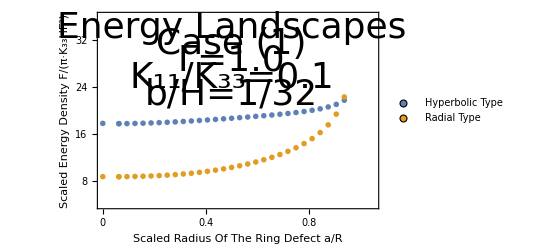

```mathematica
ee=e*Table[{1,4},{i,0,30}];
ff=f*Table[{1,4},{i,0,30}];
ListPlot[{ee,ff},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{8,16,24,32,40},None},{{0,0.2, 0.4, 0.6, 0.8,1},None}}, PlotRange->{{0,1.05},{4,36}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"Hyperbolic Type","Radial Type"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Right, Bottom}],Epilog->{Text[Style["Energy Landscapes",Directive[Black,36]],{0.5,34}],Text[Style["Case (1)",Directive[Black,36]],{0.5,31.2}],Text[Style["Γ=1.0",Directive[Black,36]],{0.5,28.4}],
Text[Style["K_11/K_33=0.1",Directive[Black,36]],{0.5,25.6}],
Text[Style["b/H=1/32",Directive[Black,36]],{0.5,22.8}]}]
```